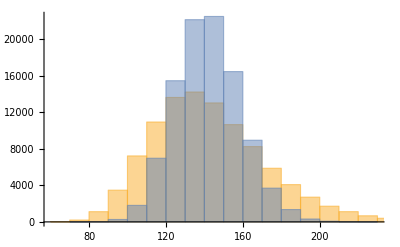

```mathematica
path=NotebookDirectory[];
n=10^4;

(*wczytanie plików*)
danielVanillaMatrix=Import[path<>"cross_daniel_short.dat"];
covNonVanilla=Import[path<>"daniel_covariance_short.dat"];
shapeInv=Import[path<>"shape_matrix_short_inv.dat"];crossDaniel=Flatten@Transpose[danielVanillaMatrix];

(*losowanie n losowych wektorów z macierzy kowariancji i z rozkładu chi2*)
dataRaw=RandomVariate[MultinormalDistribution[crossDaniel,covNonVanilla],n];
chi2=RandomVariate[ChiSquareDistribution[142],n];

(*normalizowanie wszystkich wektorów do sumy wektora wyników*)
data=(Normalize[#,Total]&/@dataRaw)*Total[crossDaniel];

(*liczenie chi2*)
result=(data[[#]]-crossDaniel).shapeInv.(data[[#]]-crossDaniel)&/@Range[n];

(*rysowanie histogramu*)
Histogram[<|"result"-> result,"chi2"-> chi2|>,LegendAppearance->"Column",ChartLegends->Automatic]
```